# MPEX helicon dispersion analysis (radial profile)

## Open Additional files:

## Get dispersion routines by evaluating Disper.nb Get plotting and printing routines by evaluating PlotPack.nb Set Parameters by opening a Parameter Window Note: Slab profile models defined in initialization cells at the bottom of this notebook.

## Load Utilities

```mathematica
utilityDir = FileNameJoin[{ParentDirectory[NotebookDirectory[]], "Plasma_Dispersion_Utilities"}];
plasmaDispersionNotebook = FileNameJoin[{utilityDir, "Plasma_Dispersion.nb"}];
plotPackNotebook = FileNameJoin[{utilityDir, "PlotPack.nb"}];
If[!FileExistsQ[plasmaDispersionNotebook] || !FileExistsQ[plotPackNotebook], Print["Could not find Plasma_Dispersion.nb or PlotPack.nb in ", utilityDir]; Abort[]];
Quiet[ClearAll[Global`PPComplexListPlot, Global`ComplexVectorListPlot, Global`rootSort, Global`paramPrint]];
Quiet[NotebookEvaluate[plasmaDispersionNotebook, InsertResults -> False, EvaluationElements -> "InitializationCell"]];
Quiet[NotebookEvaluate[plotPackNotebook, InsertResults -> False, EvaluationElements -> "InitializationCell"]];
Global`PPComplexListPlot[args___] := PlotPack`PPComplexListPlot[args];
Global`ComplexVectorListPlot[args___] := PlotPack`ComplexVectorListPlot[args];
Global`rootSort[args___] := PlotPack`rootSort[args];
Global`paramPrint[args___] := PlotPack`paramPrint[args];
If[DownValues[ColdDis0] === {} || DownValues[ColdDis2FS] === {} || DownValues[WarmDis6] === {} || DownValues[DisFuncGeneral] === {} || DownValues[PlotPack`rootSort] === {}, Print["Utility load failed; evaluate Plasma_Dispersion.nb and PlotPack.nb manually, then re-run this notebook."]; Abort[]];
```

## MPEX Setup

```mathematica
xProfileMin = 0.;
xProfileMax = 0.07;
nXmin = 1.*10^20;
nXmax = 1.*10^17;
BXmin = 0.05;
BXmax = 0.05;
TXmin = 0.002;
TXmax = 0.010;
dataSet = "mpex_helicon_radial";
xmin = xProfileMin;
xmax = xProfileMax;
nPoints = 301;
freq = 13.56;
c = 3.*10^8;
k0 = 2*Pi*freq*10^6/c;
nz = 10;
kz = nz*k0;
etaList = {0., 1., 0., 0., 0.};
TList = {1., 0., 1., 0., 0., 0.};
modelList = {1, 0, 1, 0, 0, 0};
maxharm = 5;
nminList = {-1, -maxharm, -maxharm, -maxharm, -maxharm, -maxharm};
nmaxList = {1, maxharm, maxharm, maxharm, maxharm, maxharm};
ClearAll[nprof, bprof, tprof, nprof2, bprof2, tprof2, mpexEta];
mpexEta[x_] := Clip[(x - xProfileMin)/(xProfileMax - xProfileMin), {0, 1}];
bprof2[x_?NumericQ] := BXmin;
nprof2[x_?NumericQ] := nXmin*Exp[Log[nXmax/nXmin]*mpexEta[x]^2];
tprof2[x_?NumericQ] := TXmin + mpexEta[x]*(TXmax - TXmin);
bprof[x_?NumericQ] := bprof2[x];
nprof[x_?NumericQ] := nprof2[x];
tprof[x_?NumericQ] := tprof2[x];
q = 1.6*10^-19;
mi = 2*1.67*10^-27;
me = 9.1*10^-31;
ep0 = 8.854*10^-12;
w = freq*2*Pi*10^6;
wci = q*bprof[x]/mi;
wce = q*bprof[x]/me;
wpe = Sqrt[nprof[x]*q^2/(ep0*me)];
dh = Plot[5/Mod[Abs[1 - w/wci], 1], {x, xProfileMin, xProfileMax}, PlotRange -> {0.01, 2*10^3}, PlotStyle -> Green, AxesLabel -> {"r (m)", "5/|1-w/wci|"}];
mpexRadialPlotRange = {{xProfileMin, xProfileMax}, All};
mpexRootAxesOrigin = {xProfileMin, 0.};
mpexRootAxesLabel = {Style["r (m)", FontSize -> 24], Style["n_perp", FontSize -> 24]};
```

## First Do Cold Plasma

### Plot Real and Imaginary parts of nx from 2nd order warm plasma dispersion relation (i.e. E_‖≡0)

{0.,4769.37}

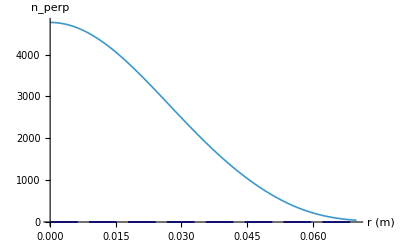

dataSet=mpex_helicon_radial

xProfileMin=0.

xProfileMax=0.07

nXmin=1.×10^20

nXmax=1.×10^17

BXmin=0.05

BXmax=0.05

freq=13.56

nz=10

etaList={0.,1.,0.,0.,0.}

xmin=0.

xmax=0.07

```mathematica
nPerpCold[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
     ColdDis0[freq,ne,b,nz,etaList]]
nt=Table[{x,nPerpCold[x]},{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
N[nt[[1]]]
PPComplexListPlot[nt,"r (m)","n_perp"]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

```mathematica
Null
```

## Plot Real and Imaginary parts of nx from 4nd order cold plasma dispersion relation (i.e. fast and slow)

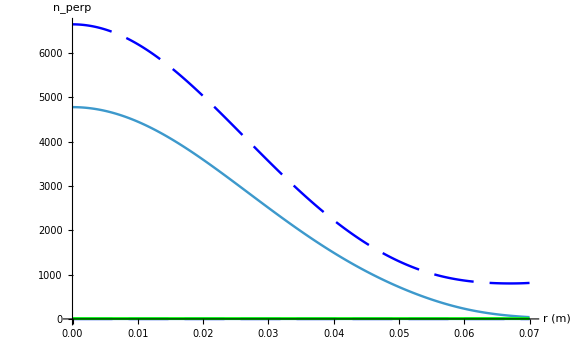

-Graphics-

dataSet=mpex_helicon_radial

xProfileMin=0.

xProfileMax=0.07

nXmin=1.×10^20

nXmax=1.×10^17

BXmin=0.05

BXmax=0.05

freq=13.56

nz=10

etaList={0.,1.,0.,0.,0.}

xmin=0.

xmin=0.

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		ColdDis2FS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=PPComplexListPlot[nF,"r (m)","n_perp"];
g2=PPComplexListPlot[nS,"r (m)","n_perp"];

xx= Transpose[nS][[1]];
reF=( Re[Transpose[nF][[2]]]);
imF=( Im[Transpose[nF][[2]]]);
reS=( Re[Transpose[nS][[2]]]);
imS=( Im[Transpose[nS][[2]]]);
reSqF=(reF^2 - imF^2);
imSqF = 2*reF*imF;
reSqS=(reS^2 - imS^2);
imSqS = 2*reS*imS;

thickness=0.01;
(*d1=ListLinePlot[{Transpose[{xx,reSqF}],Transpose[{xx,imSqF}],Transpose[{xx,reSqS}],Transpose[{xx,imSqS}]},PlotStyle->{{Black,Thickness[thickness],Opacity[0.5]},{Black,Dashed,Thickness[thickness],Opacity[0.5],CapForm["Butt"]},{Red,Thickness[thickness],Opacity[0.5]},{Red,Dashed,Thickness[thickness],Opacity[0.5],CapForm["Butt"]}},(*ScalingFunctions->"Log",*)PlotLegends->{"re(fast)[cold]","im(fast)[cold]","re(slow)[cold]","im(slow)[cold]"},AxesLabel->{"r (m)","k_perp [1/m]"},LabelStyle->"Subtitle" ];
Show[{d1,dh},ImageSize->Large, PlotRange->{0,3000}]*)

Show[{g1,g2,dh}, PlotRange->mpexRadialPlotRange,AxesOrigin->mpexRootAxesOrigin, ImageSize->Large,TicksStyle->Large,AxesLabel->mpexRootAxesLabel]
Show[{g1,g2,dh}, PlotRange->mpexRadialPlotRange,AxesOrigin->mpexRootAxesOrigin, ImageSize->Large,TicksStyle->Large,AxesLabel->mpexRootAxesLabel]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

```mathematica
Null
```

## Now Warm Plasma Stuff

### Plot Real and Imaginary parts of nx from 6th order warm plasma dispersion relation (expanded to 2nd order in k_⌊ρ)

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dataSet=mpex_helicon_radial

xProfileMin=0.

xProfileMax=0.07

nXmin=1.×10^20

nXmax=1.×10^17

BXmin=0.05

BXmax=0.05

freq=13.56

nz=10

etaList={0.,1.,0.,0.,0.}

TList={1.,0.,1.,0.,0.,0.}

modelList={1,0,1,0,0,0}

xmin=0.

xmax=0.07

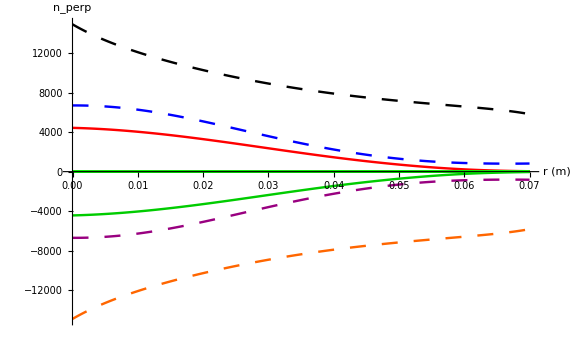

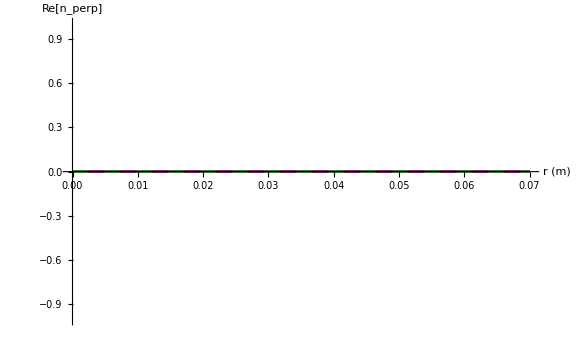

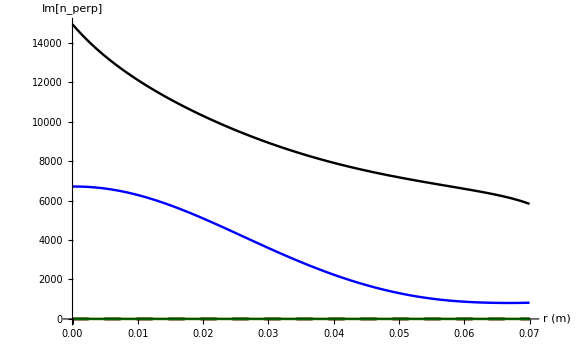

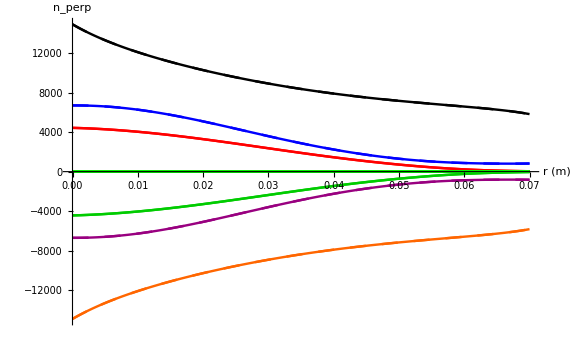

```mathematica
nPerpWarm6[x_]:=Module[{ne,te,b,x0,TL},x0=x;ne=nprof[x0];b=bprof[x0];TL=tprof[x0] *TList; WarmDis6[freq,ne,b,nz,etaList,TL]]

nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];
rootsRe=Table[Flatten[{roots[[i]][[1]],Table[Re[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];
rootsIm=Table[Flatten[{roots[[i]][[1]],Table[Im[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];



g6=ComplexVectorListPlot[roots,"r (m)","n_perp"];

paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TList, modelList,xmin,xmax}];
Show[{g6,dh},AxesOrigin->mpexRootAxesOrigin,PlotRange->mpexRadialPlotRange, ImageSize->Large,TicksStyle->Large,AxesLabel->mpexRootAxesLabel]
g7=ComplexVectorListPlot[rootsRe, "r (m)", "Re[n_perp]"]
g8 =ComplexVectorListPlot[rootsIm, "r (m)", "Im[n_perp]"]
Show[{g6,g7,g8,dh}, PlotRange->mpexRadialPlotRange,AxesOrigin->mpexRootAxesOrigin, ImageSize->Large,TicksStyle->Large,AxesLabel->mpexRootAxesLabel]
```

```mathematica
Null
```

^3

## Now Try with Hot Plasma Dispersion using root finder

```mathematica
ClearAll[nPerpHot];
nPerpHot[x_?NumericQ, nxGuess_] := Module[{ne, b, x0, TL, nx0, rootRule, rootValue},
  x0 = x;
  nx0 = nxGuess;
  ne = nprof[x0];
  b = bprof[x0];
  TL = tprof[x0]*TList;
  rootRule = Quiet[
    Check[
      FindRoot[
        DisFuncGeneral[freq, ne, b, nz, nx, etaList, TL, nminList, nmaxList, modelList],
        {nx, nx0},
        MaxIterations -> 200
      ],
      {nx -> Indeterminate},
      {FindRoot::jsing, FindRoot::nlnum, FindRoot::fdss, FindRoot::frns}
    ],
    {General::munfl, FindRoot::lstol, FindRoot::cvmit}
  ];
  rootValue = nx /. rootRule;
  If[NumericQ[N[rootValue]], rootValue, Indeterminate]
]
```

### First try root finding on warm plasma dispersion rel (model = 1)

```mathematica
modelList = {1, 0, 1, 0, 0, 0};
```

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

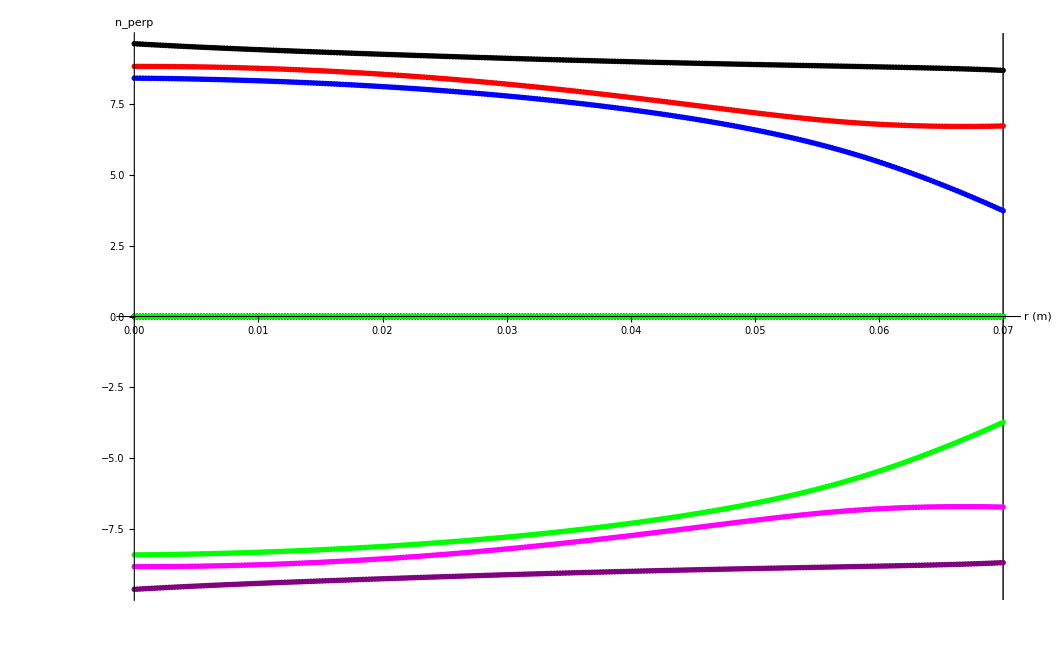

dataSet=mpex_helicon_radial

xProfileMin=0.

xProfileMax=0.07

nXmin=1.×10^20

nXmax=1.×10^17

BXmin=0.05

BXmax=0.05

freq=13.56

nz=10

etaList={0.,1.,0.,0.,0.}

TList={1.,0.,1.,0.,0.,0.}

modelList={1,0,1,0,0,0}

xmin=0.

xmax=0.07

```mathematica
nxhot[iRoot_]:=Module[{iRoot0,nxWarm,rootsWarm,nxH,x0,ne,b,t,TL},
nxWarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
iRoot0=iRoot;
rootsWarm=rootSort[nxWarm];
nxH=Table[0.,{i,1,nPoints}];
Do[
(x0=xmin+(i-1)(xmax-xmin)/(nPoints-1);
nxGuess=rootsWarm[[i]][[iRoot0+1]];
(*Print["x0 = ", x0,"  nxGuess= ",nxGuess];*)
nxH[[i]]={x0,nPerpHot[x0,nxGuess]};),{i,1,nPoints}];
nxH];


MatrixForm[nxhot[1]];
xx=nxhot[1][[All,1]];
reR1=Re[nxhot[1][[All,2]]];
imR1=Im[nxhot[1][[All,2]]];
reR2=Re[nxhot[2][[All,2]]];
imR2=Im[nxhot[2][[All,2]]];
reR3=Re[nxhot[3][[All,2]]];
imR3=Im[nxhot[3][[All,2]]];
reR4=Re[nxhot[4][[All,2]]];
imR4=Im[nxhot[4][[All,2]]];
reR5=Re[nxhot[5][[All,2]]];
imR5=Im[nxhot[5][[All,2]]];
reR6=Re[nxhot[6][[All,2]]];
imR6=Im[nxhot[6][[All,2]]];
symsize1=10;
symsize2=6;
symlog={Function[x,Sign[x] (Log[Abs[x]+1])],Function[y,Sign[y] (Exp[Abs[y]]-1)]};

d3=ListPlot[{Transpose[{xx,reR1}],Transpose[{xx,reR2}],Transpose[{xx,reR3}],Transpose[{xx,reR4}],Transpose[{xx,reR5}],Transpose[{xx,reR6}],
Transpose[{xx,imR1}],Transpose[{xx,imR2}],Transpose[{xx,imR3}],Transpose[{xx,imR4}],Transpose[{xx,imR5}],Transpose[{xx,imR6}]},
PlotStyle->{{Black},{Red},{Blue},{Purple},{Magenta},{Green},{Dashed,Black},{Dashed,Red},{Dashed,Blue},{Dashed,Purple},{Dashed,Magenta},{Dashed, Green}},
PlotMarkers->{{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2}},
PlotRange->mpexRadialPlotRange,AxesOrigin->mpexRootAxesOrigin, ImageSize->Large,TicksStyle->Large,AxesLabel->mpexRootAxesLabel,ScalingFunctions->symlog,
Epilog->{(*add vertical lines*)InfiniteLine[{xProfileMax,0},{0,1}](*,InfiniteLine[{xProfileMax,0},{0,1}],InfiniteLine[{xProfileMax,0},{0,1}]*)}];
Show[{d3}] 

paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TList,modelList,xmin,xmax}];
```

```mathematica
Null
```

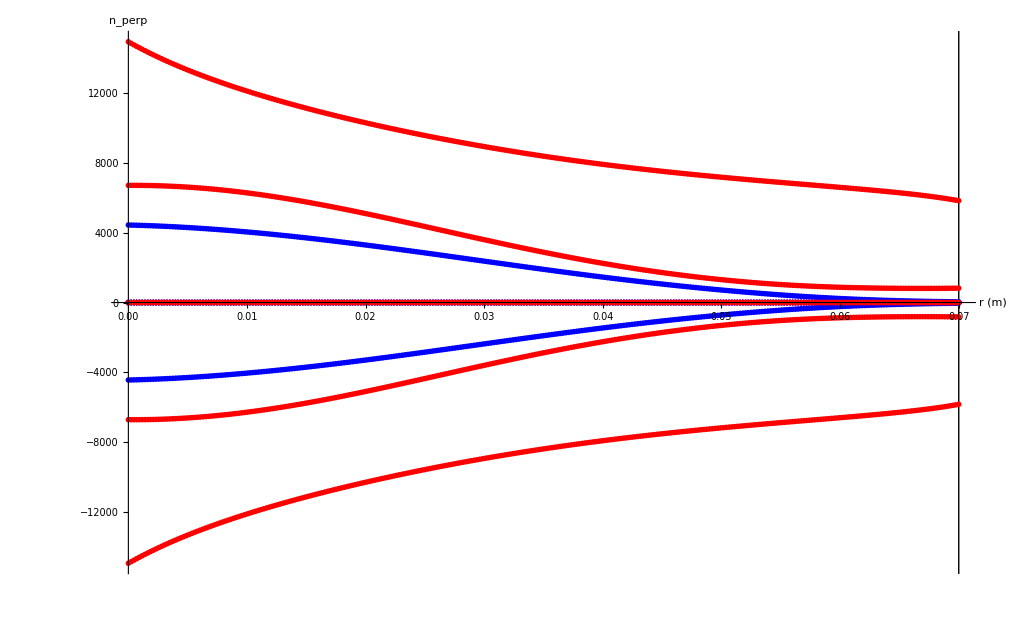

```mathematica
d3=ListPlot[{Transpose[{xx,reR1}],Transpose[{xx,reR2}],Transpose[{xx,reR3}],Transpose[{xx,reR4}],Transpose[{xx,reR5}],Transpose[{xx,reR6}],
Transpose[{xx,imR1}],Transpose[{xx,imR2}],Transpose[{xx,imR3}],Transpose[{xx,imR4}],Transpose[{xx,imR5}],Transpose[{xx,imR6}]},
PlotStyle->{{Blue},{Blue},{Blue},{Blue},{Blue},{Blue},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed, Red}},
PlotMarkers->{{"o",symsize1},{"o",symsize1},{"o",symsize1},{"o",symsize1},{"o",symsize1},{"o",symsize1},{"o",symsize2},{"o",symsize2},{"o",symsize2},{"o",symsize2},{"o",symsize2},{"o",symsize2}},
PlotRange->mpexRadialPlotRange,AxesOrigin->mpexRootAxesOrigin, ImageSize->Large,TicksStyle->Large,AxesLabel->mpexRootAxesLabel,(*ScalingFunctions->symlog,*)
Epilog->{(*add vertical lines*)InfiniteLine[{xProfileMax,0},{0,1}](*,InfiniteLine[{xProfileMax,0},{0,1}],InfiniteLine[{xProfileMax,0},{0,1}]*)}];
Show[{d3}]
```

#### Now try with hot plasma (model = 2) for active MPEX species. Can I find the warm plasma roots with the full dispersion relation?

```mathematica
xPoint=0.;
guesses=nPerpWarm6[xPoint]  (* Warm plasma roots at x=0  *)
```

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.+14941. ⅈ,0.+6713.47 ⅈ,4440.58,0.-14941. ⅈ,0.-6713.47 ⅈ,-4440.58}

```mathematica
Null
```

Change model to 2

```mathematica
modelList = {2, 0, 2, 0, 0, 0};
```

```mathematica
{nPerpHot[xPoint,guesses[[1]]],
nPerpHot[xPoint,guesses[[2]]],
nPerpHot[xPoint,guesses[[3]]],
nPerpHot[xPoint,guesses[[4]]],
nPerpHot[xPoint,guesses[[5]]],
nPerpHot[xPoint,guesses[[6]]]}
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TList,modelList,xmin,xmax}];
```

{0.+14086.6 ⅈ,-7.53337×10^-22+4502.71 ⅈ,1978.52+0. ⅈ,0.-14086.6 ⅈ,7.53337×10^-22-4502.71 ⅈ,-1978.52+0. ⅈ}

dataSet=mpex_helicon_radial

xProfileMin=0.

xProfileMax=0.07

nXmin=1.×10^20

nXmax=1.×10^17

BXmin=0.05

BXmax=0.05

freq=13.56

nz=10

etaList={0.,1.,0.,0.,0.}

TList={1.,0.,1.,0.,0.,0.}

modelList={2,0,2,0,0,0}

xmin=0.

xmax=0.07

```mathematica
Null
```

Hot plasma root finder gets all roots.  What about at xmin?

Hot plasma root finder gets 2 of the roots

### Plot hot plasma vs x

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

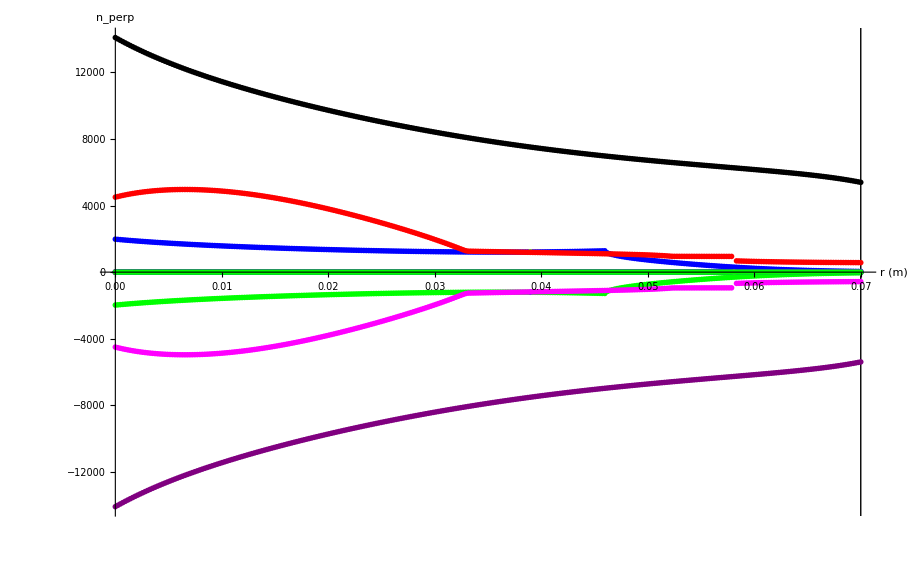

```mathematica
MatrixForm[nxhot[1]];
xx=nxhot[1][[All,1]];
reR1=( Re[nxhot[1][[All,2]]]);
imR1=( Im[nxhot[1][[All,2]]]);
reR2=( Re[nxhot[2][[All,2]]]);
imR2=( Im[nxhot[2][[All,2]]]);
reR3=( Re[nxhot[3][[All,2]]]);
imR3=( Im[nxhot[3][[All,2]]]);
reR4=( Re[nxhot[4][[All,2]]]);
imR4=( Im[nxhot[4][[All,2]]]);
reR5=( Re[nxhot[5][[All,2]]]);
imR5=( Im[nxhot[5][[All,2]]]);
reR6=( Re[nxhot[6][[All,2]]]);
imR6=( Im[nxhot[6][[All,2]]]);

reSqR1 = reR1^2 - imR1^2;
reSqR2 = reR2^2 - imR2^2;
reSqR3 = reR3^2 - imR3^2;
reSqR4 = reR4^2 - imR4^2;
reSqR5 = reR5^2 - imR5^2;
reSqR6 = reR6^2 - imR6^2;

imSqR1 = 2*reR1*imR1;
imSqR2 = 2*reR2*imR2;
imSqR3 = 2*reR3*imR3;
imSqR4 = 2*reR4*imR4;
imSqR5 = 2*reR5*imR5;
imSqR6 = 2*reR6*imR6;


symsize1=10;
symsize2=8;
symlog={Function[x,Sign[x] (Log[Abs[x]+1])],Function[y,Sign[y] (Exp[Abs[y]]-1)]};

d4=ListPlot[{Transpose[{xx,reR1}],Transpose[{xx,reR2}],Transpose[{xx,reR3}],Transpose[{xx,reR4}],Transpose[{xx,reR5}],Transpose[{xx,reR6}],
Transpose[{xx,imR1}],Transpose[{xx,imR2}],Transpose[{xx,imR3}],Transpose[{xx,imR4}],Transpose[{xx,imR5}],Transpose[{xx,imR6}]},
PlotStyle->{{Black},{Red},{Blue},{Purple},{Magenta},{Green},{Dashed,Black},{Dashed,Red},{Dashed,Blue},{Dashed,Purple},{Dashed,Magenta},{Dashed, Green}},
PlotMarkers->{{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2}},
PlotRange->mpexRadialPlotRange,AxesOrigin->mpexRootAxesOrigin, ImageSize->Large,TicksStyle->Large,AxesLabel->mpexRootAxesLabel,(*ScalingFunctions->symlog,*)
Epilog->{(*add vertical lines*)InfiniteLine[{xProfileMax,0},{0,1}](*,InfiniteLine[{xProfileMax,0},{0,1}],InfiniteLine[{xProfileMax,0},{0,1}]*)}];
Show[{d4}]
```

```mathematica
Null
```

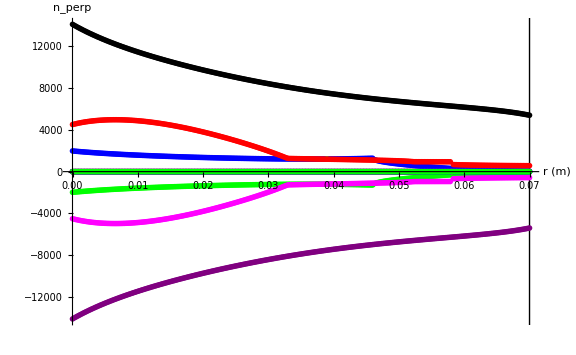

```mathematica
d4=ListPlot[{Transpose[{xx,reR1}],Transpose[{xx,reR2}],Transpose[{xx,reR3}],Transpose[{xx,reR4}],Transpose[{xx,reR5}],Transpose[{xx,reR6}],
Transpose[{xx,imR1}],Transpose[{xx,imR2}],Transpose[{xx,imR3}],Transpose[{xx,imR4}],Transpose[{xx,imR5}],Transpose[{xx,imR6}]},
PlotStyle->{{Black},{Red},{Blue},{Purple},{Magenta},{Green},{Dashed,Black},{Dashed,Red},{Dashed,Blue},{Dashed,Purple},{Dashed,Magenta},{Dashed, Green}},
PlotMarkers->{{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2}},
PlotRange->mpexRadialPlotRange,AxesOrigin->mpexRootAxesOrigin, ImageSize->Large,TicksStyle->Large,AxesLabel->mpexRootAxesLabel,(*ScalingFunctions->symlog,*)
Epilog->{(*add vertical lines*)InfiniteLine[{xProfileMax,0},{0,1}](*,InfiniteLine[{xProfileMax,0},{0,1}],InfiniteLine[{xProfileMax,0},{0,1}]*)}];
Show[{d4}]
```

## Focus on the damping

```mathematica
nxhotIm[iRoot_]:=Module[{iRoot0,nxWarm,rootsWarm,nxH,x0,ne,b,t,TL},
nxWarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
iRoot0=iRoot;
rootsWarm=rootSort[nxWarm];
nxH=Table[0.,{i,1,nPoints}];
Do[
(x0=xmin+(i-1)(xmax-xmin)/(nPoints-1);
nxGuess=rootsWarm[[i]][[iRoot0+1]];
(*Print["x0 = ", x0,"  nxGuess= ",nxGuess];*)
nxH[[i]]={x0,Im[nPerpHot[x0,nxGuess]]};),{i,1,nPoints}];
nxH];
```

#### X - mode

### O - mode

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

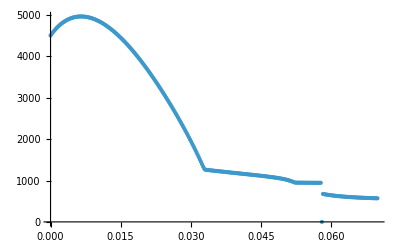

General::munfl: Exp[-5.40493×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.33811×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

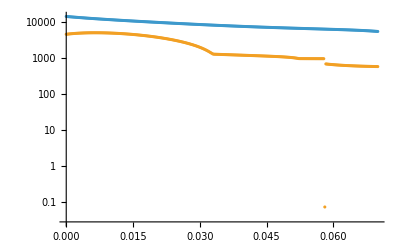

```mathematica
ListPlot[nxhotIm[2]]
ListPlot[{nxhotIm[1],nxhotIm[2]},ScalingFunctions->"Log",PlotRange->{{xProfileMin,xProfileMax},All}]
```

```mathematica
Null
```

## Plot Profiles

```mathematica
Plot[nprof[x],{x,xmin,xmax}]
```

-Graphics-

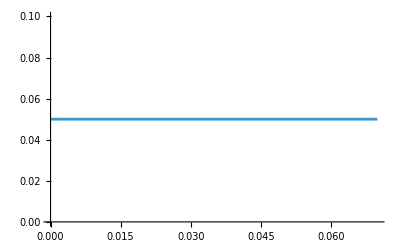

```mathematica
Plot[bprof[x],{x,xmin,xmax}]
```

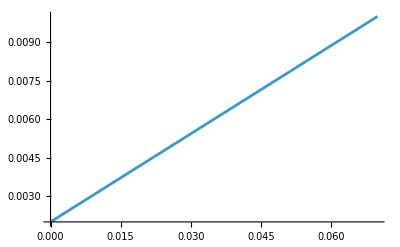

```mathematica
Plot[tprof[x],{x,xmin,xmax}]
```

## Initialization

#### Magnetic field,Density and Temperature Profiles

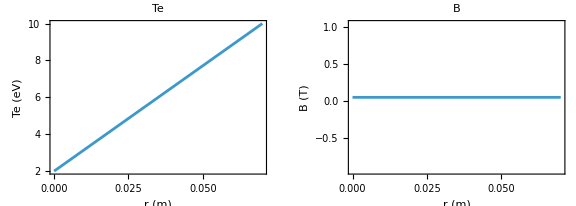
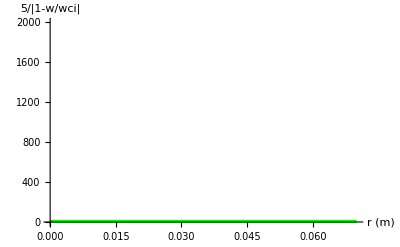
r (m) | ne (m^-3) | Te (eV) | B (T)
0. | 1.×10^20 | 2. | 0.05
0.07 | 1.×10^17 | 10. | 0.05
-Graphics-
-Graphics-

```mathematica
ClearAll[nprof, bprof, tprof, nprof2, bprof2, tprof2, mpexEta];
mpexEta[x_?NumericQ] := Clip[(x - xProfileMin)/(xProfileMax - xProfileMin), {0, 1}];
bprof2[x_?NumericQ] := BXmin;
nprof2[x_?NumericQ] := nXmin*Exp[Log[nXmax/nXmin]*mpexEta[x]^2];
tprof2[x_?NumericQ] := TXmin + mpexEta[x]*(TXmax - TXmin);
bprof[x_?NumericQ] := bprof2[x];
nprof[x_?NumericQ] := nprof2[x];
tprof[x_?NumericQ] := tprof2[x];
wci = q*bprof[x]/mi;
wce = q*bprof[x]/me;
wpe = Sqrt[nprof[x]*q^2/(ep0*me)];
dh = Plot[5/Mod[Abs[1 - w/wci], 1], {x, xProfileMin, xProfileMax}, PlotRange -> {0.01, 2*10^3}, PlotStyle -> Green, AxesLabel -> {"r (m)", "5/|1-w/wci|"}];
mpexRadialPlotRange = {{xProfileMin, xProfileMax}, All};
mpexRootAxesOrigin = {xProfileMin, 0.};
mpexRootAxesLabel = {Style["r (m)", FontSize -> 24], Style["n_perp", FontSize -> 24]};
profileSummary = Grid[Prepend[Table[{r, nprof[r], 1000*tprof[r], bprof[r]}, {r, {xProfileMin, xProfileMax}}], {"r (m)", "ne (m^-3)", "Te (eV)", "B (T)"}], Frame -> All];
profilePlots = GraphicsRow[{Plot[nprof[x], {x, xProfileMin, xProfileMax}, PlotRange -> All, Frame -> True, Axes -> False, FrameLabel -> {"r (m)", "ne (m^-3)"}, PlotLabel -> "ne"], Plot[1000*tprof[x], {x, xProfileMin, xProfileMax}, PlotRange -> All, Frame -> True, Axes -> False, FrameLabel -> {"r (m)", "Te (eV)"}, PlotLabel -> "Te"], Plot[bprof[x], {x, xProfileMin, xProfileMax}, PlotRange -> All, Frame -> True, Axes -> False, FrameLabel -> {"r (m)", "B (T)"}, PlotLabel -> "B"]}, ImageSize -> Large];
Column[{profileSummary, profilePlots, dh}]
```